### ALL

```mathematica
SetDirectory[NotebookDirectory[]];
<<Initialisation.m;
```

```mathematica
(*Let's create some large amount of numeric data*)
DeformationProbes=Table[{0.5, 0.1*i}, {i, 0, 10}];
k=200;
DeformationProbesP=SetPrecision[DeformationProbes, 3k];

Do[FctData[i]=MyBWNumeric[DeformationProbesP[[i,1]], DeformationProbesP[[i,2]],0, k];
PertData[i]=MyBWSeries[FctData[i]];
, {i, 1, Length[DeformationProbes]}]
```

```mathematica
(*Save the data to some file*)
SetDirectory[NotebookDirectory[]];
ExportFile= "PertDataRange.m";

(*A header*)
Outstring="This data was created with the following parameters:";
Export[ExportFile, Outstring];
Save[ExportFile, k]
Save[ExportFile, DeformationProbes]

(*The big stuff*)
Save[ExportFile, PertData]
```

### Playground

{{10,0.453125},{20,1.01563},{30,2.625},{40,5.25},{50,9.32813}}

FittedModel[0.0305235 x+2.02922×10^-6 x^2+0.0000624785 x^3]

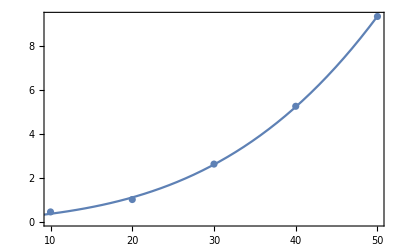

{{x→-100.563-175.558 ⅈ},{x→-100.563+175.558 ⅈ},{x→201.093}}

```mathematica
(*Let's estimate how long computations take*)
DeformationProbes={{0.2, 0.4}, {0.35, 0.4}, {0.38, 0.4}, {0.39, 0.4}, {0.395, 0.4}, {0.4, 0.4}, {0.41, 0.4}};
zin=0.38`40;
ein=0.4`40;
ttest[n_]:=Timing[BW=MyBWNumeric[zin,ein,0,n]][[1]]
end=50;
data=Table[{n, ttest[n]}, {n, 10, end, 10}]

lm=NonlinearModelFit[data,a1 x+a2 x^2+a3 x^3 , {a0, a1, a2, a3, a4}, x]
Show[ListPlot[data],Plot[lm[x],{x,0,end}],Frame->True]

NSolve[Normal[lm]==3600/7, x]
```

```mathematica
(*The numeric computations using the power series of V agree with the "exact" ones:*)
zin=0.38`40;
ein=0.4`40;
a=MyBWSeries[MyBWNumeric[zin,ein,0,4]]
b=MyBWSeries[MyBW[zin, ein, 0, 4]]
a-b
```